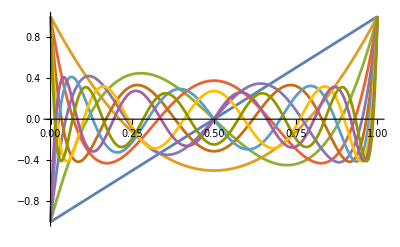

```mathematica
Plot[Evaluate@Table[LegendreP[k,(2x-1)],{k,1,10}],{x,0,1}]
```

```mathematica
Clear[λ,k]
λ[k_]:=k(k+1)
```

```mathematica
(* Legendre polynomials satisfy this differential equation in the unit interval*)
D[x(1-x)D[LegendreP[k,(2x-1)],x],x]+λ[k]*LegendreP[k,(2x-1)]//FullSimplify
```

0